# Kelvin problem in 2-d plane strain

Define the relevant functions that are needed for integrating the response to a point force

```mathematica
x = xo - xs;
y = yo - ys;
C0 = 1/ (4 * Pi *(1-ν));
r = Sqrt[x^2 + y^2];
g = -C0 * Log[r];
gx = -C0*x/r^2;
gy = -C0*y/r^2;
gxy = 2*C0*x*y/r^4;
gxx = C0*(x^2 - y^2)/r^4;
gyy = -gxx;
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) 
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy)
sxx = fx*(2*(1 - ν)*gx - x*gxx) + fy*(2*ν* gy - y*gxx);
syy = fx*(2*ν*gx - x*gyy) + fy * (2*(1 - ν)*gy - y*gyy);
sxy = fx*((1 - 2*ν)*gy - x*gxy) + fy*((1 - 2*ν)*gx - y*gxy);
```

-(fy (xo-xs) (-yo+ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs) (yo-ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fy ((yo-ys)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

```mathematica
ux0 = ReplaceAll[ux,{ys->0,yo->0}]
uy0 = ReplaceAll[uy,{ys->0,yo->0}]
```

(fx (1/(4 π (1-ν))-((3-4 ν) Log[√((xo-xs)^2)])/(4 π (1-ν))))/(2 μ)

-(fy (3-4 ν) Log[√((xo-xs)^2)])/(8 π μ (1-ν))

```mathematica
uxInt0 = Integrate[ux0,{xs,-1,1},Assumptions->{Im[xo]==0}]
uyInt0 = Integrate[uy0,{xs,-1,1},Assumptions->{Im[xo]==0}]
```

-(fx (2+1/2 (-3+4 ν) (-4-(-1+xo) Log[(-1+xo)^2]+(1+xo) Log[(1+xo)^2])))/(8 π μ (-1+ν))

(fy (-3+4 ν) (4-2 xo ArcTanh[(2 xo)/(1+xo^2)]+Log[1/((-1+xo^2)^2)]))/(16 π μ (-1+ν))

### First compute indefinite integral and then evaluate at the end points to get definite integral

```mathematica
UxIndef = Integrate[ux,xs,GeneratedParameters->C];
UxDef = ReplaceAll[UxIndef,{xs->1}]-ReplaceAll[UxIndef,{xs->-1}]//FullSimplify
```

-1/(16 π μ (-1+ν))(-16 fx (-1+ν)-8 fx (yo-ys) (-1+ν) ArcTan[(-1+xo)/(yo-ys)]+8 fx (yo-ys) (-1+ν) ArcTan[(1+xo)/(yo-ys)]+fx (-3+4 ν) Log[(-1+xo)^2+(yo-ys)^2]+(fy (-yo+ys)+fx xo (3-4 ν)) Log[1+(-2+xo) xo+(yo-ys)^2]+fx (-3+4 ν) Log[(1+xo)^2+(yo-ys)^2]+(fy (yo-ys)+fx xo (-3+4 ν)) Log[1+xo (2+xo)+(yo-ys)^2])

```mathematica
UyIndef = Integrate[uy,xs,GeneratedParameters->C];
UyDef = ReplaceAll[UyIndef,{xs->1}]-ReplaceAll[UyIndef,{xs->-1}]//FullSimplify
```

-1/(16 π μ (-1+ν))(-2 fy (3-4 ν) (-1+xo+(-yo+ys) ArcTan[(-1+xo)/(yo-ys)])+2 fy (3-4 ν) (1+xo+(-yo+ys) ArcTan[(1+xo)/(yo-ys)])+fy (-1+xo) (3-4 ν) Log[(-1+xo)^2+(yo-ys)^2]+fy (1+xo) (-3+4 ν) Log[(1+xo)^2+(yo-ys)^2]+(fy √(-(yo-ys)^2)+fx (-yo+ys)) Log[-1+xo-√(-(yo-ys)^2)]+(fx (yo-ys)-fy √(-(yo-ys)^2)) Log[1+xo-√(-(yo-ys)^2)]-(fx (yo-ys)+fy √(-(yo-ys)^2)) Log[-1+xo+√(-(yo-ys)^2)]+(fx (yo-ys)+fy √(-(yo-ys)^2)) Log[1+xo+√(-(yo-ys)^2)])

## Check numerical solution versus analytical solution

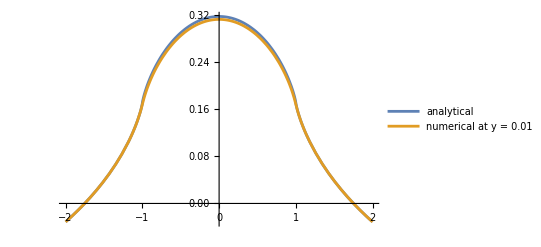

```mathematica
Plot[{ReplaceAll[uxInt0,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[UxDef,{fx->1,fy->0,μ->1,ν->0.25,ys->0,yo->0.01}]},{xo,-2,2},PlotLegends->{"analytical","numerical at y = 0.01"}]
```

## Plot analytical solutions for U_x and U_y (f_x = 1)

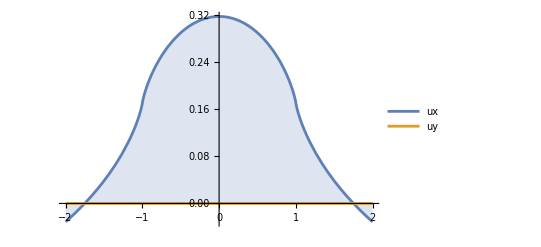

```mathematica
Plot[ {ReplaceAll[uxInt0,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[uyInt0,{fx->1,fy -> 0, μ->1,ν->0.25}]},{xo,-2,2},Filling->Axis,PlotLegends->{"ux","uy"}]
```

## Plot analytical solutions for U_x and U_y (f_y = -1)

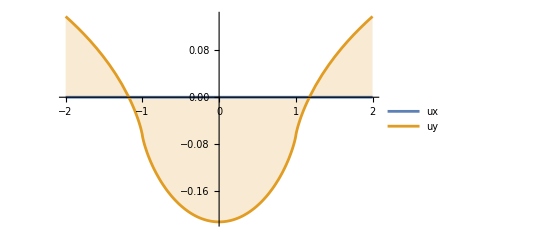

```mathematica
Plot[ {ReplaceAll[uxInt0,{fx -> 0,fy->-1, μ->1,ν->0.25}],ReplaceAll[uyInt0,{fx->0,fy -> -1, μ->1,ν->0.25}]},{xo,-2,2},Filling->Axis,PlotLegends->{"ux","uy"}]
```

## Plot numerical solution for U_x and U_y in 2-d

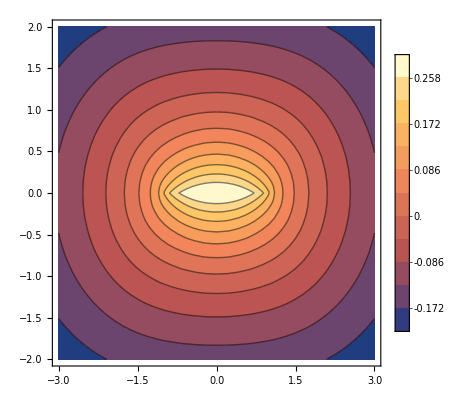

```mathematica
ContourPlot[ReplaceAll[UxDef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->Automatic,Contours->11]
```

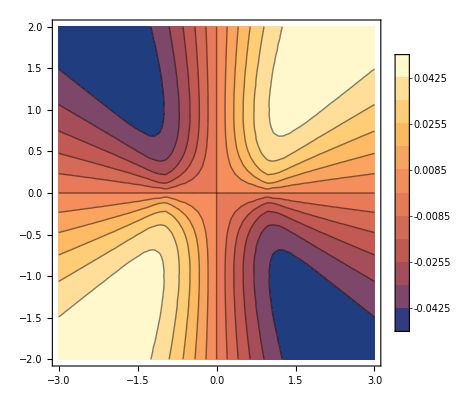

```mathematica
ContourPlot[ReplaceAll[UyDef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->Automatic,Contours->11]
```

## Linearly varying force along line element 1. Displacements

```mathematica
uxLinIndefInt0 = Integrate[ReplaceAll[ux*(Subscript[a, 0] + Subscript[a, 1]*xs),{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
uyLinIndefInt0 = Integrate[ReplaceAll[uy*(Subscript[a, 0] + Subscript[a, 1]*xs),{ys->0}],xs,GeneratedParameters->C]//FullSimplify;
uxLinDefInt0 = ReplaceAll[uxLinIndefInt0,{xs->w}] -  ReplaceAll[uxLinIndefInt0,{xs->-w}]//FullSimplify
uyLinDefInt0 = ReplaceAll[uyLinIndefInt0,{xs->w}] -  ReplaceAll[uyLinIndefInt0,{xs->-w}]//FullSimplify
```

1/(32 π μ (-1+ν))(2 (8 fx (-1+ν) (w+yo ArcTan[(-w+xo)/yo])+(fy yo+fx (-w+xo) (-3+4 ν)) Log[(w-xo)^2+yo^2]) a_0-2 (-8 fx (-1+ν) (w-yo ArcTan[(w+xo)/yo])+(fy yo+fx (w+xo) (-3+4 ν)) Log[(w+xo)^2+yo^2]) a_0+(w (4 fy yo+fx w (-5+4 ν)+fx xo (-6+8 ν))+4 yo (fy yo+4 fx xo (-1+ν)) ArcTan[(-w+xo)/yo]+(2 fy xo yo+fx (w^2 (3-4 ν)+yo^2 (5-4 ν)+xo^2 (-3+4 ν))) Log[(w-xo)^2+yo^2]) a_1-(w (-4 fy yo+fx (6 xo-8 xo ν+w (-5+4 ν)))+4 yo (fy yo+4 fx xo (-1+ν)) ArcTan[(w+xo)/yo]+(2 fy xo yo+fx (w^2 (3-4 ν)+yo^2 (5-4 ν)+xo^2 (-3+4 ν))) Log[(w+xo)^2+yo^2]) a_1)

1/(32 π μ (-1+ν))(2 (2 fy w (-3+4 ν)+4 fy yo (-1+2 ν) ArcTan[(-w+xo)/yo]+(fx yo+fy (-w+xo) (-3+4 ν)) Log[(w-xo)^2+yo^2]) a_0-2 (2 fy w (3-4 ν)+4 fy yo (-1+2 ν) ArcTan[(w+xo)/yo]+(fx yo+fy (w+xo) (-3+4 ν)) Log[(w+xo)^2+yo^2]) a_0+(w (4 fx yo+fy (w+2 xo) (-3+4 ν))+4 yo (fx yo+2 fy xo (-1+2 ν)) ArcTan[(-w+xo)/yo]+(2 fx xo yo+fy (3 w^2+yo^2-4 (w^2+yo^2) ν+xo^2 (-3+4 ν))) Log[(w-xo)^2+yo^2]) a_1-(-4 fx w yo+fy w (w-2 xo) (-3+4 ν)+4 yo (fx yo+2 fy xo (-1+2 ν)) ArcTan[(w+xo)/yo]+(2 fx xo yo+fy (3 w^2+yo^2-4 (w^2+yo^2) ν+xo^2 (-3+4 ν))) Log[(w+xo)^2+yo^2]) a_1)

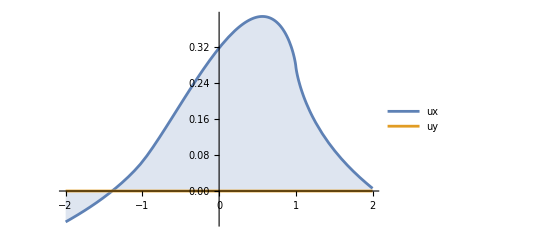

```mathematica
Plot[ {ReplaceAll[uxLinDefInt0,{fx -> 1,fy->0, μ->1,ν->0.25,w->1,Subscript[a, 0]->1,Subscript[a, 1]->1,yo->0.00001}],ReplaceAll[uyLinDefInt0,{fx -> 1,fy->0, μ->1,ν->0.25,w->1,Subscript[a, 0]->1,Subscript[a, 1]->1,yo->0.00001}]},{xo,-2,2},Filling->Axis,PlotLegends->{"ux","uy"}]
```

## 2. Stresses

```mathematica
sxyLinIndefInt0 = Integrate[ReplaceAll[sxy*(Subscript[a, 0] + Subscript[a, 1]*xs),{ys->0,fy->0}],xs,GeneratedParameters->C]//FullSimplify;
sxxLinIndefInt0 = Integrate[ReplaceAll[sxx*(Subscript[a, 0] + Subscript[a, 1]*xs),{ys->0,fy->0}],xs,GeneratedParameters->C]//FullSimplify;
syyLinIndefInt0 = Integrate[ReplaceAll[syy*(Subscript[a, 0] + Subscript[a, 1]*xs),{ys->0,fy->0}],xs,GeneratedParameters->C]//FullSimplify;
```

```mathematica
sxyLinDefInt0 = ReplaceAll[sxyLinIndefInt0,{xs->w}] -  ReplaceAll[sxyLinIndefInt0,{xs->-w}]
sxxLinDefInt0 = ReplaceAll[sxxLinIndefInt0,{xs->w}] -  ReplaceAll[sxxLinIndefInt0,{xs->-w}]//FullSimplify;
syyLinDefInt0 = ReplaceAll[syyLinIndefInt0,{xs->w}] -  ReplaceAll[syyLinIndefInt0,{xs->-w}]//FullSimplify;
```

-(fx yo (1/2 (-3+2 ν) Log[(-w+xo)^2+yo^2] a_1+(2 (-1+ν) ArcTan[(w-xo)/yo] (a_0+xo a_1))/yo+((w-xo) a_0-(-w xo+xo^2+yo^2) a_1)/((-w+xo)^2+yo^2)))/(4 π (-1+ν))+(fx yo (1/2 (-3+2 ν) Log[(w+xo)^2+yo^2] a_1+(2 (-1+ν) ArcTan[(-w-xo)/yo] (a_0+xo a_1))/yo+((-w-xo) a_0-(w xo+xo^2+yo^2) a_1)/((w+xo)^2+yo^2)))/(4 π (-1+ν))

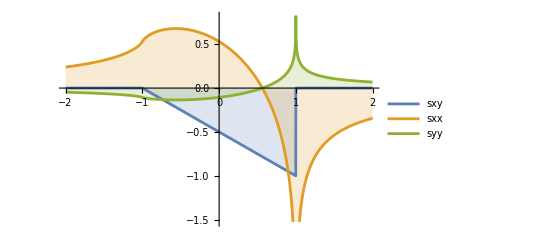

```mathematica
Plot[ {ReplaceAll[sxyLinDefInt0,{fx -> 1,fy->0, μ->1,ν->0.25,w->1,Subscript[a, 0]->1,Subscript[a, 1]->1,yo->0.000001}],ReplaceAll[sxxLinDefInt0,{fx -> 1,fy->0, μ->1,ν->0.25,w->1,Subscript[a, 0]->1,Subscript[a, 1]->1,yo->0.0000001}],
ReplaceAll[syyLinDefInt0,{fx -> 1,fy->0, μ->1,ν->0.25,w->1,Subscript[a, 0]->1,Subscript[a, 1]->1,yo->0.00000001}]},
{xo,-2,2},Filling->Axis,PlotLegends->{"sxy","sxx","syy"}]
```